```mathematica
Δϵ=2;
```

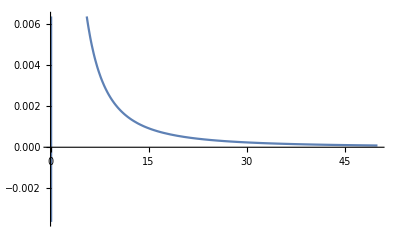

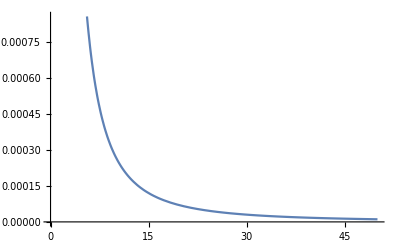

```mathematica
pDR1and[R1_, ϵ1_, ϵ2_, R2_, p_,n_, ωab_] := (R1/n Exp[-ϵ1] + R1/n Exp[-ϵ1] R2/n  Exp[-ϵ2] Exp[-ωab] ) / (1 + R1/n Exp[-ϵ1] (1+p)+ R2/n Exp[-ϵ2] (1+p) +  p + R1/n Exp[-ϵ1] R2/n  Exp[-ϵ2] Exp[-ωab]); 
pDR2and[R1_, ϵ1_, ϵ2_, R2_, p_,n_, ωab_] := (R2/n Exp[-ϵ2] + R1/n Exp[-ϵ1] R2/n  Exp[-ϵ2] Exp[-ωab]  ) / (1 + R1/n Exp[-ϵ1] (1+p)+ R2/n Exp[-ϵ2] (1+p) +  p + R1/n Exp[-ϵ1] R2/n  Exp[-ϵ2] Exp[-ωab]); 
HDR1and[R1_, ϵ1_, ϵ2_, R2_, p_, n_, ωab_] = D[pDR1and[R1, ϵ1+Δϵ, ϵ2, R2, p, n, ωab]-pDR1and[R1, ϵ1, ϵ2, R2,p, n, ωab], R1];
HDR2and[R1_, ϵ1_, ϵ2_, R2_, p_, n_, ωab_] = D[pDR2and[R1, ϵ1, ϵ2+Δϵ, R2, p, n, ωab]-pDR2and[R1, ϵ1, ϵ2, R2, p, n, ωab], R1];
Plot[HDR1and[R1, -14, -14, 25, 5000/(4.5*10^6) *Exp[5], 4.5*10^6, -5],{R1,0,50}]
Plot[HDR2and[R1, -14, -14, 25, 5000/(4.5*10^6) *Exp[5], 4.5*10^6, -5],{R1,0,50}]
```

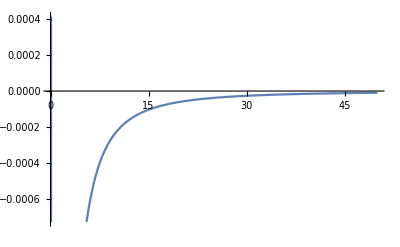

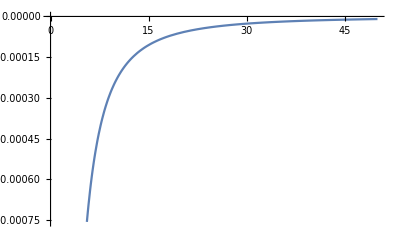

```mathematica
pDRor[R1_, ϵ1_, ϵ2_, R2_, p_,n_, ωab_] := 1 / (1 + R1/n Exp[-ϵ1] + R2/n Exp[-ϵ2] +  p + R1/n Exp[-ϵ1] R2/n  Exp[-ϵ2]Exp[-ωab]); 
HDRor1[R1_, ϵ1_, ϵ2_, R2_, p_, n_, ωab_] = D[pDRor[R1, ϵ1+Δϵ, ϵ2, R2, p, n, ωab]-pDRor[R1, ϵ1, ϵ2, R2,p, n,ωab], R1];
HDRor2[R1_, ϵ1_, ϵ2_, R2_, p_, n_, ωab_] = D[pDRor[R1, ϵ1, ϵ2+Δϵ, R2, p, n, ωab]-pDRor[R1, ϵ1, ϵ2, R2, p, n, ωab], R1];
Plot[HDRor1[R1, -14, -14, 25, 5000/(4.5*10^6) *Exp[5], 4.5*10^6, -5],{R1,0,50}]
Plot[HDRor2[R1, -14, -14, 25, 5000/(4.5*10^6) *Exp[5], 4.5*10^6, -5],{R1,0,50}]
```

```mathematica
pa[A1_, ϵ1_, ϵ2_, A2_, p_,n_, ωa1_, ωa2_,  ωa1a2_] := (A1/n Exp[-ϵ1] * Exp[-ωa1] + A2/n Exp[-ϵ2]* Exp[-ωa2]  +   A2/n Exp[-ϵ2]* A1/n Exp[-ϵ1]* Exp[-ωa1a2]*Exp[-ωa1]* Exp[-ωa2] + 1) / (p*(A1/n Exp[-ϵ1] * Exp[-ωa1] + A2/n Exp[-ϵ2]* Exp[-ωa2]  +   A2/n Exp[-ϵ2]* A1/n Exp[-ϵ1]* Exp[-ωa1a2]*Exp[-ωa1]* Exp[-ωa2] + 1)
+ A1/n Exp[-ϵ1]  + A2/n Exp[-ϵ2] +   A2/n Exp[-ϵ2]* A1/n Exp[-ϵ1]* Exp[-ωa1a2]+ 1);
```

```mathematica
HA1[A1_, ϵ1_, ϵ2_, A2_, p_,n_, ωa1_, ωa2_,  ωa1a2_]= N[D[pa[A1, ϵ1+Δϵ, ϵ2, A2, p,n, ωa1, ωa2,  ωa1a2]-pa[A1, ϵ1, ϵ2, A2, p,n, ωa1, ωa2,  ωa1a2], A1]];
HA2[A1_, ϵ1_, ϵ2_, A2_, p_,n_, ωa1_, ωa2_,  ωa1a2_] = N[D[pa[A1, ϵ1, ϵ2+Δϵ, A2, p,n, ωa1, ωa2,  ωa1a2]-pa[A1, ϵ1, ϵ2, A2, p,n, ωa1, ωa2,  ωa1a2], A1]];
```

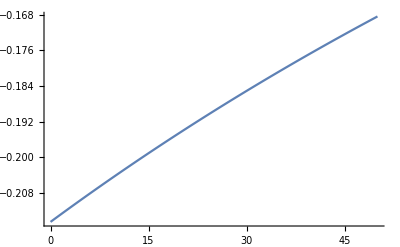

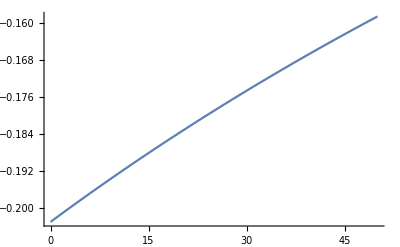

```mathematica
Plot[HA1[A1, -7, -7, 25, (4600/(4.5*10^6)) *Exp[2], 4.5*10^6,-4, -4,  -4],{A1,0,50}]
Plot[HA2[A1, -7, -7, 25, (4600/(4.5*10^6)) *Exp[2], 4.5*10^6,-4, -4,  -4],{A1,0,50}]
```

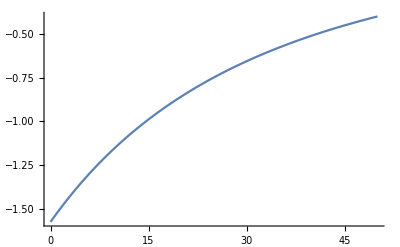

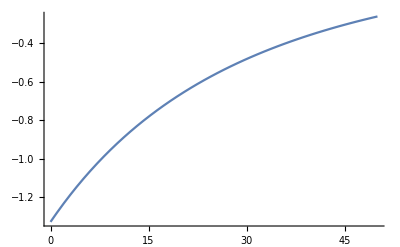

```mathematica
Plot[HA1[A1, -7, -7, 25, (4600/(4.5*10^6)) *Exp[2], 4.5*10^6,-7, -7,  0],{A1,0,50}]
Plot[HA2[A1, -7, -7, 25, (4600/(4.5*10^6)) *Exp[2], 4.5*10^6,-7, -7,  0],{A1,0,50}]
```